```mathematica
XY = {{0., 0.8}, {0.2,0.85}, {0.4,0.825}, {0.6, 0.9},{0.8, 0.5}};
```

```mathematica
Y = Interpolation[XY, InterpolationOrder->2]
```

InterpolatingFunction[…]

```mathematica
Y[0.]
```

0.8

```mathematica
Y[0.4]
```

0.825

```mathematica
v = {{1,0,0},{1, 0.2, 0.2^2}, {1, 0.4, 0.4^2}};
G = {0.8, 0.85 , 0.825};
```

```mathematica
Ai = LinearSolve[v, G]
```

{0.8,0.4375,-0.9375}

```mathematica
Clear[z]
```

```mathematica
pol1 = 0.8 +0.4375z-0.9375z^2;
```

```mathematica
Clear[v, G]
```

```mathematica
v = {{1, 0.4, 0.16},{1, 0.6, 0.6^2}, {1, 0.8, 0.8^2}};
G = {0.825, 0.9, 0.5};
```

```mathematica
LinearSolve[v, G]
```

{-0.75,6.3125,-5.9375}

```mathematica
pol2 = -0.75 + 6.3125z-5.9375z^2;
```

```mathematica
p1 = Plot[pol1, {z, 0, 0.4}, PlotRange->{{0,1},{0, 1}}];
p2 = Plot[pol2, {z, 0.4, 1}, PlotRange->{0, 1}];
```

```mathematica
p3 = Plot[0.8+1.66667z -11.7188z^2+27.0833z^3-19.5313z^4, {z, 0, 1}, PlotRange->{0, 1}];
```

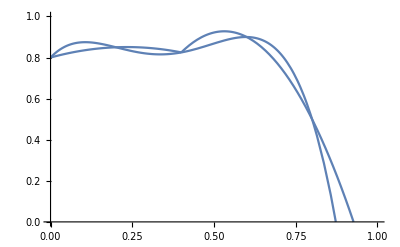

```mathematica
Show[p1, p2, p3]
```

```mathematica
X = {0.05, 0.2, 0.4, 0.6, 0.8};
```

```mathematica
Y = {0.8, 0.85, 0.825, 0.9, 0.5};
```

```mathematica
m = 5;
```

```mathematica
S = Array[s, {m,m}]; n = Length[X];
```

```mathematica
z = Table[Sum[X[[i]]^(j)/n, {i,n}], {j , 0, 2*(m-1)}]
```

Power::indet: Indeterminate expression 0.^0 encountered.

{Indeterminate,0.4,0.24,0.16,0.11328,0.0832,0.062592,0.047872,0.0370452}

```mathematica
z[[1]] = 1;
```

```mathematica
z
```

{1,0.4,0.24,0.16,0.11328,0.0832,0.062592,0.047872,0.0370452}

```mathematica
TA = Table[s[i,j]=z[[i+j-1]], {i,m}, {j,m}];
```

```mathematica
b = Table[Sum[X[[i]]^j*Y[[i]]/n, {i,n}], {j, 0 ,(m-1)}]
```

Power::indet: Indeterminate expression 0.^0 encountered.

{Indeterminate,0.288,0.162,0.102,0.068784}

```mathematica
b[[1]]=Y[[1]]/n;
```

```mathematica
b
```

{0.16,0.288,0.162,0.102,0.068784}

```mathematica
A = Inverse[TA].b
```

{-2.275,33.6979,-123.828,187.24,-99.6094}

```mathematica
Clear[p]
```

```mathematica
pol4[p_]:= -2.274999999999686+33.69791666663809p-123.82812499982538p^2+187.23958333299015p^3-99.60937499978536p^4
```

```mathematica
pol4[p]
```

-2.275+33.6979 p-123.828 p^2+187.24 p^3-99.6094 p^4

```mathematica
TT = {{0.1*10^-20,0.8},{0.2,0.85},{0.4,0.825},{0.6,0.9},{0.8,0.5}}
```

{{1.×10^-21,0.8},{0.2,0.85},{0.4,0.825},{0.6,0.9},{0.8,0.5}}

Set::write: Tag Plus in (-1.95286+12.7286 p-12.4107 p^2)[arg_] is Protected.

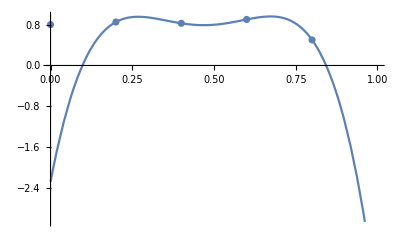

```mathematica
Show[Plot[pol4[p], {p,0 ,1}], ListPlot[TT]]
```

```mathematica
TT = Transpose[{X, Y}]
```

{{0.,0.8},{0.2,0.85},{0.4,0.825},{0.6,0.9},{0.8,0.5}}

```mathematica
Is = Sum[(pol4[TT[[i,1]]]-TT[[i,2]])^2, {i, 1,n}]/n
```

1.89112